```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/778nm.dat"]
```

{{1.65577,-0.0947613},{1.59352,-0.0905923},{1.51672,-0.0957513},{1.46373,-0.062993},{1.42047,-0.0594846},{1.37769,-0.0629824},{1.34607,-0.0527575},{1.31418,-0.0665245},{1.27734,-0.0725062},{1.24989,-0.0782967},{1.21939,-0.0630357},{1.20221,-0.0781778},{1.18519,-0.169579},{1.17023,-0.261053},{1.1572,-0.299593},{1.14604,-0.360912},{1.13497,-0.442171},{1.12762,-0.903449},{1.12192,-0.708687},{1.11852,-0.669763},{1.11638,-0.628465},{1.11532,-0.553925},{1.11466,-0.251324},{1.11691,-0.160568},{1.12052,-0.0775508},{1.12514,-0.0407282},{1.15252,-0.0367988},{1.18204,-0.0782318},{1.20774,0.00697561},{1.24068,-0.00765926},{1.28541,0.00139902},{1.36328,-0.00702461},{1.4246,-0.00242293}}

-1.18187+0.785039 x

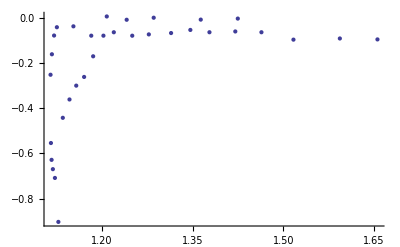

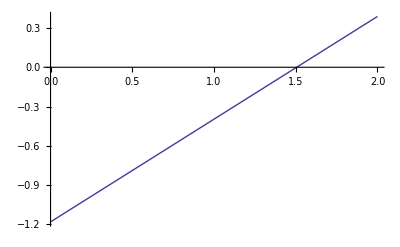

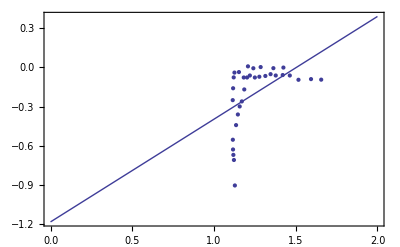

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```